```mathematica
This code produces directed reflexive graphs.
Written by Eric Johnson at FOCUS | numeric.
```

-Graphics-

{-Graphics-,-Graphics-}

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0)

48

{1->2,1->8,1->10,1->14,2->2,2->3,2->11,3->2,3->7,3->13,4->2,4->4,4->14,5->1,5->3,5->5,5->7,5->9,5->15,6->9,6->11,6->14,7->1,7->9,7->12,7->13,8->4,9->1,9->6,9->12,9->14,10->2,10->4,10->7,10->10,10->12,11->11,11->14,12->7,12->8,12->11,13->2,13->11,13->15,14->1,14->6,15->12,15->13}

15

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

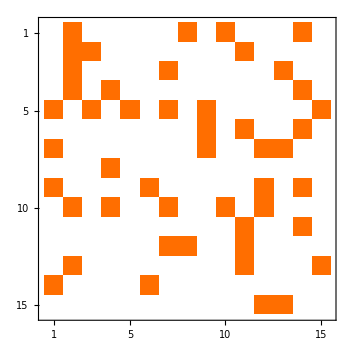

{2.84777,-1.65049,1.44016+0.49539 ⅈ,1.44016-0.49539 ⅈ,1.05375+0.56543 ⅈ,1.05375-0.56543 ⅈ,-1.0351,1.,-0.787607+0.406796 ⅈ,-0.787607-0.406796 ⅈ,-0.229609+0.837405 ⅈ,-0.229609-0.837405 ⅈ,0.173163+0.743698 ⅈ,0.173163-0.743698 ⅈ,0.538109}

5.

3.

3-7 t+3 t^2-6 t^4+8 t^5+5 t^6-7 t^7+8 t^8-16 t^9-2 t^10+25 t^11-14 t^12-4 t^13+5 t^14-t^15

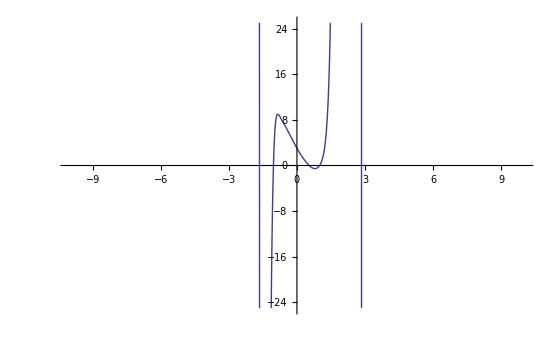

{4.43833×10^-10,-1.81899×10^-12,-3.41061×10^-13-(7.10543×10^-14) ⅈ,-3.41061×10^-13+(7.10543×10^-14) ⅈ,1.42109×10^-14-(1.77636×10^-14) ⅈ,1.42109×10^-14+(1.77636×10^-14) ⅈ,-1.77636×10^-14,0.,7.10543×10^-15-(4.44089×10^-16) ⅈ,7.10543×10^-15+(4.44089×10^-16) ⅈ,0.+(3.55271×10^-15) ⅈ,0.-(3.55271×10^-15) ⅈ,0.+(1.11022×10^-15) ⅈ,0.-(1.11022×10^-15) ⅈ,-9.02056×10^-17}

```mathematica
n=15;
Clear A;
Clear G;
MatA=Table[Random[Integer,{0,RandomInteger[]}],{i,1,n},{j,1,n}];
MatD=MatrixForm[UpperTriangularize[MatA]];
AD=DiagonalMatrix[Diagonal[MatA]];
A = MatA;
G=AdjacencyGraph[A,VertexLabels->"Name",ImagePadding->10,ImageSize->550]
Table[AdjacencyGraph[A,GraphLayout->l,PlotLabel->l,ImageSize->350,VertexLabels->"Name"],{l,{"CircularEmbedding","SpiralEmbedding"}}]
MatrixForm[A]
EdgeCount[G]
EdgeList[G]
VertexCount[G]
VertexList[G]
MatrixPlot[A,ImageSize->350]
1.*Eigenvalues[A]
1.*Tr[A]
1.*Det[A]
PA[t_]=CharacteristicPolynomial[A,t]
Plot[PA[t],{t,-5,5},PlotRange->{{-10,10},{-25,25}},ImageSize->550]
ScientificForm[PA[1.Eigenvalues[A]]]
```